## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
<<IGraphM`
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"BigSur 8.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"Additional Bioinformatics Functions.nb"}]];
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

ReplacePart::argrx: ReplacePart called with 2 arguments; 3 arguments are expected.

```mathematica
lowcRows[l_,min_]:=With[{x=Transpose[l]},Select[Range[Length[x]],Total[x[[#]]]>=min&]];
lowExRows[mat_, x_]:= Module[{means},
means = Mean/@mat;
Select[Range[Length[means]],means[[#]]>=x&]
];
```

## Load data

```mathematica
smallTest = Import["../testthat/fixtures/test_counts.mtx"];
```

```mathematica
smallTestGenes = Import["../testthat/fixtures/test_Genes.csv"][[2;;]];
```

```mathematica
smallTestCells = Import["../testthat/fixtures/test_Cells.csv"][[2;;]];
```

```mathematica
Dimensions[smallTest]
```

{254,250}

```mathematica
smallTestMatpac = {smallTest, smallTestGenes, smallTestCells};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
rajFull = Import["../testthat/fixtures/arjunrajrawcounts2.mtx"];
rajGenes = Import["../testthat/fixtures/arjunrajgenenames2.csv"];
rajCells = Import["../testthat/fixtures/arjunrajcellnames2.csv"];
```

```mathematica
kcells= lowcRows[rajFull,1300];
```

```mathematica
Length[kcells]
```

3117

```mathematica
kgenes = lowExRows[rajFull, 0.001];
```

```mathematica
Length[kgenes]
```

14695

```mathematica
Min[Total/@rajFull]
```

8

```mathematica
rajMatpac = {rajFull[[kgenes,kcells]], Flatten[rajGenes][[kgenes]], Flatten[rajCells][[kcells]]};
```

```mathematica
raj2k = {rajMatpac[[1]][[1;;2000]], rajMatpac[[2]][[1;;2000]],rajMatpac[[3]]};
```

```mathematica
Export["raj2k.mx",raj2k];
```

```mathematica
Dimensions/@rajMatpac
```

{{14695,3117},{14695},{3117}}

```mathematica
Export["../testthat/fixtures/rajSubs.mtx",rajMatpac[[1]]];
Export["../testthat/fixtures/rajSubGenes.csv",rajMatpac[[2]]];
Export["../testthat/fixtures/rajSubCells.csv", rajMatpac[[3]]];
```

## Residuals, eta/theta, and c’s

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

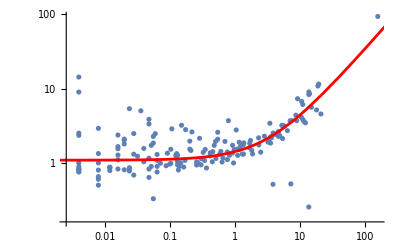

```mathematica
etaTheta=Values@TwoComponentCL1[smallTestMatpac, 250];
```

```mathematica
Export["etaTheta.txt", etaTheta]
```

etaTheta.txt

```mathematica
TwoComponentCL1All[matpac_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
newmat=mat;
newgenetotals=genetotals;
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

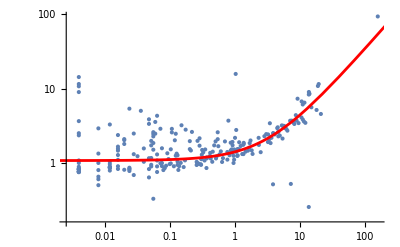

{0.0797936,0.331465}

```mathematica
etaTheta=Values@TwoComponentCL1All[smallTestMatpac]
```

```mathematica
Export["etaTheta.txt", etaTheta]
```

etaTheta.txt

```mathematica
TwoComponentCL1AllThetaOnly[matpac_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
newmat=mat;
newgenetotals=genetotals;
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
Print[Length[data]];
params=FindFit[Log[data], {Log[1+ θ*E^x],{ θ>0}},  {{θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

```mathematica
Options[TwoComponentCThetaOnly]={"Sample Goal"-> 3000, "zero eta"->True };
TwoComponentCThetaOnly[matpac_, OptionsPattern[]]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data,stop,indices,θlist,temp, params, t1},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[OptionValue["Sample Goal"]/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
indices=Partition[RandomSample[Range[Length[newgenetotals]]], UpTo[200]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues={};θlist={};data={};
For[k=1,k<= Length[indices],k++,
fittedjvalues=Join[fittedjvalues, Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, indices[[k]]}]];
data=N[Select[Transpose[{newgenetotals[[Flatten[indices[[1;;k]]]]]/n, 1+fittedjvalues*newgenetotals[[Flatten[indices[[1;;k]]]]]/n}], Last[#]>0&]];
If[OptionValue["zero eta"],
params=Join[{η->0},FindFit[Log[data], {Log[1+ θ*E^x],θ>0},{{θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]],
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]];
AppendTo[θlist,{k,θ/.params}];
NotebookDelete[t1];NotebookDelete[stop];
t1=PrintTemporary[Last/@θlist];
NotebookDelete[temp];
temp=PrintTemporary[Grid[{{
ListPlot[θlist, Joined-> True, PlotRange-> {{1,Length[indices]},{0,Automatic}}],
Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]
}}]];
stop=PrintTemporary[Button["Stop Operation",Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
Print[{200k "genes tested", params}];FrontEndTokenExecute["EvaluatorAbort"]]];];
NotebookDelete[stop];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
{200k "genes tested", params}]
```

```mathematica
Options[TwoComponentCThetaOnlyVec]={"zero eta"->True,"Tolerance"->1.*^-12,"Max Iterations"->100};

TwoComponentCThetaOnlyVec[matpac_,OptionsPattern[]]:=Module[{mat,depthlist,n,genetotals,ematrix,a,b,lo,j,f,fp,jnew,bad,tol,maxit,k,data,params, keep, bin, counts, w},mat=matpac[[1]];
depthlist=Total/@N[Transpose[mat]]/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
ematrix=KroneckerProduct[genetotals,depthlist];
a=(mat/ematrix-1)^2;
b=1/ematrix;
lo=-(Min/@b);(*j must exceed this per gene*)tol=OptionValue["Tolerance"];
maxit=OptionValue["Max Iterations"];
j=ConstantArray[1.,Length[genetotals]];
Do[f=(Total/@(a/(b+j)))-(n-1);
fp=-(Total/@(a/(b+j)^2));
jnew=j-f/fp;
bad=UnitStep[lo-jnew];(*1 where the step leaves the domain*)jnew=(1-bad) jnew+bad (j+lo)/2;(*bisect toward the pole instead*)If[Max[Abs[jnew-j]]<tol,j=jnew;Break[]];
j=jnew,{k,maxit}];
data=Transpose[{genetotals/n,1+j*genetotals/n}];keep=Flatten@Position[Last/@data,_?Positive];data=N[data[[keep]]];bin=Floor[Log[genetotals[[keep]]]/0.5];counts=Counts[bin];w=1./Sqrt[Lookup[counts,bin]];               (*each half-log bin contributes equally*)

params=Join[{η->0},FindFit[Log[data],{Log[1+θ*E^x],θ>0},{{θ,0.1}},x,NormFunction->(Total[w*Abs[#]]&), MaxIterations->1000]];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+θ*μ)/. params,{μ,Min[First/@data],Max[First/@data]},PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{"mean expression (μ)","1+η+θμ"}]]];
{Length[genetotals] "genes tested",params}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

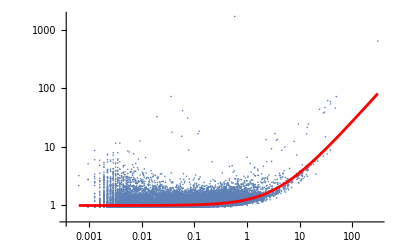

{14695 genes tested,{η→0,θ→0.261967}}

```mathematica
rajthetaOnly2=TwoComponentCThetaOnlyVec[rajMatpac]
```

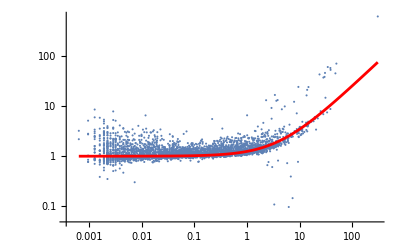

{η→0,θ→0.248263}

```mathematica
rajthetaOnly=TwoComponentCThetaOnly[rajMatpac, "Sample Goal"->5000][[2]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

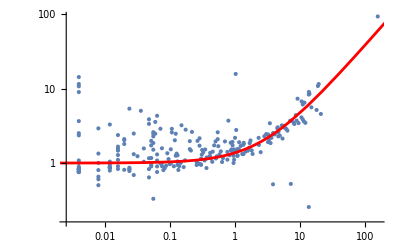

{0.369289}

```mathematica
thetaOnly=Values@TwoComponentCL1AllThetaOnly[smallTestMatpac]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

14683

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

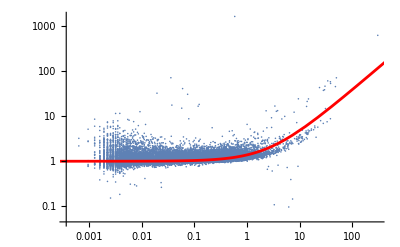

{0.382955}

```mathematica
rajTheta = Values@TwoComponentCL1AllThetaOnly[rajMatpac]
```

```mathematica
Export["thetaOnly.txt", thetaOnly]
```

thetaOnly.txt

```mathematica
Options[BigSurAlt7Test]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt7Test[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities,κ1,κ2,κ3,κ4},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
Print["Started on",CurrentDate[]];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
Share[];
ematrix = KroneckerProduct[genetotals, depthlist];
Share[];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export["residuals.csv", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Share[];
Export["mcfanos.csv", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κ1=FanoCum1[ematrix,clist,n];Share[];
	κ2=FanoCum2[ematrix,clist,n];Share[];
	κ3=FanoCum3[ematrix,clist,n];Share[];
	κ4=FanoCum4[ematrix,clist,n];Share[];
	κlists={κ1,κ2,κ3,κ4};
(*κlists=FanoCumulants5CFAlt[ematrix,clist,n];*);
Export["FK1.csv",κ1];
Export["FK2.csv",κ2];
Export["FK3.csv",κ3];
Export["FK4.csv",κ4];
Share[];
Print["Fano cumulants calculated"];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
Share[];
Print["Cornish-Fisher coefficients calculated"];
Export["FCF1.csv",polylist[[1]]];
Export["FCF2.csv",polylist[[2]]];
Export["FCF3.csv",polylist[[3]]];
Export["FCF4.csv",polylist[[4]]];
Export["FCF5.csv",polylist[[5]]];
Share[];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export["pccmatrix.csv", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentListsAltNew[genetotals,depthlist, η, θ, n];
Export["invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
Share[];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCFAlt[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Export["CK1.csv", ccmats[[1]]];
Export["CK2.csv", ccmats[[2]]];
Export["CK3.csv", ccmats[[3]]];
Export["CK4.csv", ccmats[[4]]];
]
```

```mathematica
Directory[]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
thetaOnly[[1]]
```

0.369289

```mathematica
SetDirectory[".."]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests

```mathematica
SetDirectory["RajThetaOnly"];
```

```mathematica
rajTheta[[1]]
```

0.382955

```mathematica
BigSurAlt7Test[rajMatpac,η/.rajthetaOnly2[[2]],θ/.rajthetaOnly2[[2]],"x", "Correlations"->True ]
```

Started onMon 28 Sep 2026 10:43:04GMT-7

Folder name is

foldername$61240

Modified, corrected Fano factors acquired and saved10:44:54GMT-7TimeObject[{10,44,54.215525},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 10:54:21GMT-7TimeObject[{10,54,21.627435},Instant,-7.]

inverse squareroot Fano moments acquired and saved 10:57:05GMT-7TimeObject[{10,57,5.820942},Instant,-7.]

```mathematica
SetDirectory["OneComponent"];
BigSurAlt7Test[smallTestMatpac, 0., thetaOnly[[1]],"x", "Correlations"->True ]
```

Started onFri 25 Sep 2026 16:20:55GMT-7

Folder name is

foldername$48786

Modified, corrected Fano factors acquired and saved16:20:56GMT-7TimeObject[{16,20,56.327578},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 16:20:58GMT-7TimeObject[{16,20,58.88966},Instant,-7.]

inverse squareroot Fano moments acquired and saved 16:25:13GMT-7TimeObject[{16,25,13.41612},Instant,-7.]

```mathematica
SetDirectory[".."];
(*CreateDirectory["TwoComponent"];*)
SetDirectory["TwoComponent"]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/TwoComponent

```mathematica
BigSurAlt7Test[smallTestMatpac, etaTheta[[1]], etaTheta[[2]],"x", "Correlations"->True ]
```

Started onFri 25 Sep 2026 15:59:42GMT-7

Folder name is

foldername$38926

Modified, corrected Fano factors acquired and saved15:59:43GMT-7TimeObject[{15,59,43.745868},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 15:59:46GMT-7TimeObject[{15,59,46.308736},Instant,-7.]

inverse squareroot Fano moments acquired and saved 16:04:04GMT-7TimeObject[{16,4,4.054545},Instant,-7.]

```mathematica
Export["test_Genes.csv",smallTestMatpac[[2]]]
```

test_Genes.csv

```mathematica
Context[FanoCum1]
```

Global`

```mathematica
?FanoCum1
```

## Test that results are consistent between platforms

```mathematica
theta = 0.2536582;
```

```mathematica
Directory[]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
Dimensions/@raj2k
```

{{2000,3117},{2000},{3117}}

```mathematica
BigSurAlt7[raj2k, 0., theta,"RajTest",Automatic, "Correlations"->True ]
```

Started onTue 29 Sep 2026 11:20:01GMT-7

CreateDirectory::eexist: /Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/RajTest η=0. θ=0.254 already exists.

Folder name is

RajTest η=0. θ=0.254

Part::partw: Part 4 of … does not exist.

Modified, corrected Fano factors acquired and saved11:20:02GMT-7TimeObject[{11,20,2.546012},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Polynomials constructed.

Fano p-values acquired and saved11:20:05GMT-7TimeObject[{11,20,5.703867},Instant,-7.]

Modified corrected correlations acquired and saved 11:20:05GMT-7TimeObject[{11,20,5.829993},Instant,-7.]

inverse squareroot Fano moments acquired and saved 11:22:33GMT-7TimeObject[{11,22,33.680441},Instant,-7.]

Adjusted cumulants of the correlations acquired11:22:35GMT-7TimeObject[{11,22,35.702401},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired11:22:35GMT-7TimeObject[{11,22,35.922813},Instant,-7.]

1999000 equations gathered11:22:37GMT-7TimeObject[{11,22,37.31571},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6703311:22:44GMT-7TimeObject[{11,22,44.090674},Instant,-7.]

TakeSmallestBy::tbnval: Values {31.1338,2.5025,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {41.2472,2.53462,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {37.0257,Abs[z],Abs[z],2.72888} produced by the function Abs cannot be used for numerical sorting because they are not all real.

General::stop: Further output of TakeSmallestBy::tbnval will be suppressed during this calculation.

True roots found11:22:49GMT-7TimeObject[{11,22,49.045724},Instant,-7.]

Quasiroots found 11:22:59GMT-7TimeObject[{11,22,59.17266},Instant,-7.]

x-values acquired11:22:59GMT-7TimeObject[{11,22,59.215712},Instant,-7.]

p-values acquired and saved11:22:59GMT-7TimeObject[{11,22,59.279864},Instant,-7.]

equivalent PCCs acquired and saved11:23:01GMT-7TimeObject[{11,23,1.802833},Instant,-7.]

For FDR = 0.02, the significance level is p < 6.20515×10^-4

significant PCCs identified and saved11:23:01GMT-7TimeObject[{11,23,1.837486},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved11:23:02GMT-7TimeObject[{11,23,2.06444},Instant,-7.]

Communities Identified11:23:02GMT-7TimeObject[{11,23,2.873555},Instant,-7.]

done

```mathematica
res = Import["RajTest η=0. θ=0.254/RajTest_cell-specific residuals.mx"];
fanos = Import["RajTest η=0. θ=0.254/RajTest_modified_corrected_Fano factors.mx"];
fanops = Import["RajTest η=0. θ=0.254/RajTest_fanopvalues.mx"];

pccs = Import["RajTest η=0. θ=0.254/RajTest_pccmatrix.mx"];
logps = Import["RajTest η=0. θ=0.254/RajTest_logpvalues.mx"];
```

```mathematica
pccs
```

SparseArray[…]

```mathematica
Length[pccs["ExplicitValues"]]
Count[pccs["ExplicitValues"],_?Positive]
Count[pccs["ExplicitValues"],_?Negative]
```

61451

32850

28601

```mathematica
rCorrs = Import["rCorr.mtx"];
```

```mathematica
rCorrs = LowerTriangularize[rCorrs];
```

```mathematica
rCorrs
```

SparseArray[<67685>, {2000, 2000}]

```mathematica
Length[Intersection[rCorrs["ExplicitPositions"], pccs["ExplicitPositions"]]]
```

61097

```mathematica
rRes = Import["rRes.csv","Data"][[2;;,2;;]];
```

```mathematica
rRes==res
```

False

```mathematica
Dimensions[rRes]
```

{2000,3117}

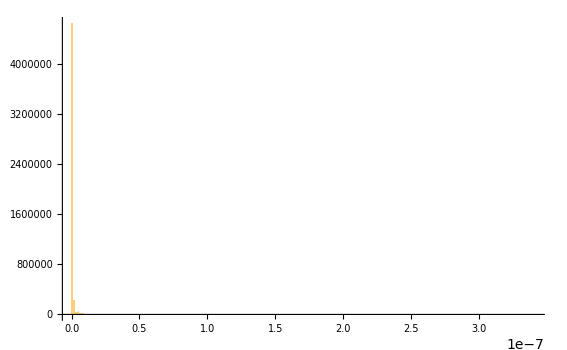

```mathematica
Histogram[Abs[Flatten[rRes-res]], PlotRange->All]
```

```mathematica
Max[Abs[Flatten[rRes-res]]]
```

3.41137×10^-7

```mathematica
rAll = Import["rAllPCC.csv","Data"][[2;;,2;;]];
```

```mathematica
Dimensions[rAll]
```

{2000,2000}

```mathematica
mcPCC=SparseArray[BoolEval[logps>-Log10[0.05]]*pccs];
```

```mathematica
mcPCC
```

SparseArray[<62925>, {2000, 2000}]

```mathematica
diffPCC=Abs[Extract[rAll,mcPCC["ExplicitPositions"]]-mcPCC["ExplicitValues"]];
```

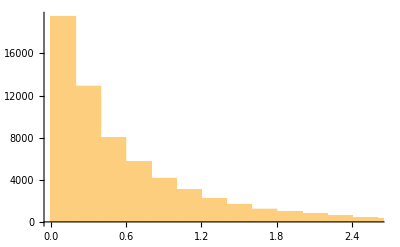

```mathematica
Histogram[diffPCC]
```

```mathematica
Max[diffPCC]
```

1.46596×10^-9

```mathematica
rmcFano = Import["rAllmcFanos.csv","Data"][[2;;,2;;]];
```

```mathematica
diffFano = Abs[Flatten[rmcFano]-Flatten[fanos]];
```

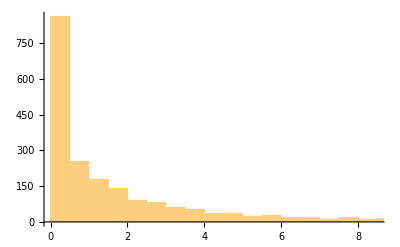

```mathematica
Histogram[diffFano]
```

```mathematica
Max[diffFano]
```

4.04306×10^-8

```mathematica
pccs[[18,11]]
```

-0.347658

```mathematica
mat=raj2k[[1]];
genetotals = Total/@mat;
n=Width[mat];
m=Length[genetotals];
clist=√(0/#+ theta)&/@N[genetotals/n];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
```

```mathematica
m1=InverseSqrtMomentListsAltNew[genetotals,depthlist,0.,theta,n];
m2=InverseSqrtMomentListsAltNew[genetotals,depthlist,0.,theta,n];
Max[Abs[Flatten[m1]/Flatten[m2]-1]]
```

0.458827

```mathematica
Max[Abs[m1[[All,All,2]]/m2[[All,All,2]]-1]]
```

0.458827

```mathematica
Quantile[Flatten[Abs[m1[[All,All,2]]/m2[[All,All,2]]-1]],{0.5,0.9,1.}]
```

{0.0104393,0.261873,0.458827}

```mathematica
BigSurAlt7[raj2k,0.,theta,"RajTest2",Automatic,"Correlations"->True]
```

Started onTue 29 Sep 2026 12:19:17GMT-7

CreateDirectory::eexist: /Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/RajTest2 η=0. θ=0.254 already exists.

Folder name is

RajTest2 η=0. θ=0.254

Part::partw: Part 4 of … does not exist.

Modified, corrected Fano factors acquired and saved12:19:18GMT-7TimeObject[{12,19,18.881823},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Polynomials constructed.

Fano p-values acquired and saved12:19:22GMT-7TimeObject[{12,19,22.035312},Instant,-7.]

Modified corrected correlations acquired and saved 12:19:22GMT-7TimeObject[{12,19,22.150058},Instant,-7.]

inverse squareroot Fano moments acquired and saved 12:21:49GMT-7TimeObject[{12,21,49.980378},Instant,-7.]

Adjusted cumulants of the correlations acquired12:21:51GMT-7TimeObject[{12,21,51.807549},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired12:21:51GMT-7TimeObject[{12,21,51.989861},Instant,-7.]

1999000 equations gathered12:21:53GMT-7TimeObject[{12,21,53.378076},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6692912:22:00GMT-7TimeObject[{12,22,0.045893},Instant,-7.]

TakeSmallestBy::tbnval: Values {31.0732,2.50353,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {41.2349,2.53836,Abs[z],Abs[z]} produced by the function Abs cannot be used for numerical sorting because they are not all real.

TakeSmallestBy::tbnval: Values {36.9994,Abs[z],Abs[z],2.73112} produced by the function Abs cannot be used for numerical sorting because they are not all real.

General::stop: Further output of TakeSmallestBy::tbnval will be suppressed during this calculation.

True roots found12:22:05GMT-7TimeObject[{12,22,5.23832},Instant,-7.]

Quasiroots found 12:22:15GMT-7TimeObject[{12,22,15.1825},Instant,-7.]

x-values acquired12:22:15GMT-7TimeObject[{12,22,15.22068},Instant,-7.]

p-values acquired and saved12:22:15GMT-7TimeObject[{12,22,15.28405},Instant,-7.]

equivalent PCCs acquired and saved12:22:17GMT-7TimeObject[{12,22,17.64646},Instant,-7.]

For FDR = 0.02, the significance level is p < 6.18591×10^-4

significant PCCs identified and saved12:22:17GMT-7TimeObject[{12,22,17.689493},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved12:22:17GMT-7TimeObject[{12,22,17.916724},Instant,-7.]

Communities Identified12:22:18GMT-7TimeObject[{12,22,18.704449},Instant,-7.]

done

```mathematica
res2 = Import["RajTest2 η=0. θ=0.254/RajTest2_cell-specific residuals.mx"];
fanos2 = Import["RajTest2 η=0. θ=0.254/RajTest2_modified_corrected_Fano factors.mx"];
fanops2 = Import["RajTest2 η=0. θ=0.254/RajTest2_fanopvalues.mx"];

pccs2 = Import["RajTest2 η=0. θ=0.254/RajTest2_significantPCCs.mx"];
logps2 = Import["RajTest2 η=0. θ=0.254/RajTest2_logpvalues.mx"];
```

```mathematica
pccs
```

SparseArray[…]

```mathematica
pccs2
```

SparseArray[…]

```mathematica
Count[10^-(logps["ExplicitValues"]),0.]
Min[Select[10^-(logps["ExplicitValues"]),#>0&]]
```

13330

5.×10^-324

```mathematica
logpmatrix = logps;
```

```mathematica
lp=-Log[10]*logpmatrix["ExplicitValues"];   (*natural log p,negative*)
nn=Length[lp];o=Ordering[lp];
adj=lp[[o]]+Log[nn]-Log[Range[nn]];
adj=Reverse[FoldList[Min,Reverse[adj]]][[;;nn]];
Count[adj,x_/;x<Log[0.02]]
```

62925

```mathematica
Length[logpmatrix["ExplicitValues"]]
Quantile[logpmatrix["ExplicitValues"],{0,.25,.5,.75,1}]
```

67033

{0.301046,113.487,196.489,255.499,1.76226×10^10}

## Bug fix on ImprovedFindXAlt

```mathematica
raj2k=Import["raj2k.mx"];
```

```mathematica
theta = 0.2536582;
```

```mathematica
BigSurAlt7[raj2k,0.,theta,"RajTest3",Automatic,"Correlations"->True]
```

Started onTue 29 Sep 2026 13:38:33GMT-7

CreateDirectory::eexist: /Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/RajTest3 η=0. θ=0.254 already exists.

Folder name is

RajTest3 η=0. θ=0.254

Part::partw: Part 4 of {SparseArray[<701720>, {2000, 3117}], <<1>>, {GCAAGTCGATAT, GGACAATTTGTA, <<3114>>, ATTCTTGTGTAC}} does not exist.

Modified, corrected Fano factors acquired and saved13:38:34GMT-7TimeObject[{13,38,34.622676},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Polynomials constructed.

Fano p-values acquired and saved13:38:38GMT-7TimeObject[{13,38,38.001627},Instant,-7.]

Modified corrected correlations acquired and saved 13:38:38GMT-7TimeObject[{13,38,38.115802},Instant,-7.]

inverse squareroot Fano moments acquired and saved 13:41:03GMT-7TimeObject[{13,41,3.472323},Instant,-7.]

Adjusted cumulants of the correlations acquired13:41:05GMT-7TimeObject[{13,41,5.236928},Instant,-7.]

Cornish Fisher Polynomial Coefficients acquired13:41:05GMT-7TimeObject[{13,41,5.3862},Instant,-7.]

1999000 equations gathered13:41:06GMT-7TimeObject[{13,41,6.728484},Instant,-7.]

Quick test complete.  Surviving parameter sets = 6768213:41:13GMT-7TimeObject[{13,41,13.27115},Instant,-7.]

True roots found13:41:15GMT-7TimeObject[{13,41,15.50646},Instant,-7.]

Quasiroots found 13:41:15GMT-7TimeObject[{13,41,15.50883},Instant,-7.]

x-values acquired13:41:15GMT-7TimeObject[{13,41,15.52888},Instant,-7.]

p-values acquired and saved13:41:15GMT-7TimeObject[{13,41,15.59265},Instant,-7.]

equivalent PCCs acquired and saved13:41:17GMT-7TimeObject[{13,41,17.62914},Instant,-7.]

For FDR = 0.02, the significance level is p < -9.43419

significant PCCs identified and saved13:41:18GMT-7TimeObject[{13,41,18.59852},Instant,-7.]

ReplaceAll::reps: {GCAAGTCGATAT,GGACAATTTGTA,TGACAATTGACC,TAAGACTTCCCT,GAAACGGACAGA,TCGATTGGAGAA,AGGAAGATTTAA,GTCTCAAAGCAC,GTACGAACATAG,GGTCGAGATATA,«3107»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gene Network Object saved13:41:18GMT-7TimeObject[{13,41,18.757792},Instant,-7.]

Communities Identified13:41:18GMT-7TimeObject[{13,41,18.974786},Instant,-7.]

done

```mathematica
res3 = Import["RajTest3 η=0. θ=0.254/RajTest3_cell-specific residuals.mx"];
fanos3 = Import["RajTest3 η=0. θ=0.254/RajTest3_modified_corrected_Fano factors.mx"];
fanops3= Import["RajTest3 η=0. θ=0.254/RajTest3_fanopvalues.mx"];

pccs3 = Import["RajTest3 η=0. θ=0.254/RajTest3_pccmatrix.mx"];
logps3 = Import["RajTest3 η=0. θ=0.254/RajTest3_logpvalues.mx"];
```

```mathematica
pccs3
```

SparseArray[…]

```mathematica
rCorrsLT
```

SparseArray[…]

```mathematica
rCorrs = Import["rCorr2.mtx"];
```

```mathematica
rCorrsLT=LowerTriangularize[rCorrs];
```

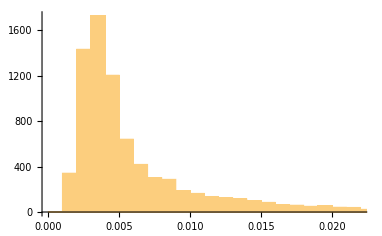

```mathematica
Histogram[Abs[rCorrsLT["ExplicitValues"]-Extract[pccs3,rCorrsLT["ExplicitPositions"]]]]
```

```mathematica
mcPCC=SparseArray[BoolEval[logps3>-Log10[0.02]]*pccs3];
```

```mathematica
Max[Abs[rCorrsLT["ExplicitValues"]-Extract[mcPCC,rCorrsLT["ExplicitPositions"]]]]
```

1.46596×10^-9

```mathematica
rPs
```

SparseArray[…]

```mathematica
logps3
```

SparseArray[<67682>, {2000, 2000}]

```mathematica
Max[Abs[rPs["ExplicitValues"]-Extract[logps3,rPs["ExplicitPositions"]]]]
```

213.146

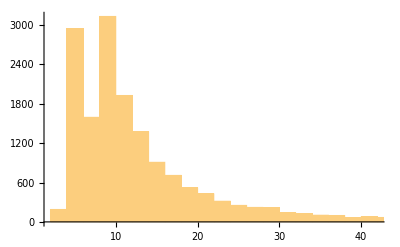

```mathematica
Histogram[Abs[rPs["ExplicitValues"]-Extract[logps3,rPs["ExplicitPositions"]]]]
```

```mathematica
Max[pccs3]
```

0.260956

```mathematica
rPs = Import["rPs2.mtx"];
```

```mathematica
Length[Intersection[rPs["ExplicitPositions"], logps3["ExplicitPositions"]]]
```

7982

```mathematica
Length[rPs["ExplicitPositions"]]/2
```

7982

```mathematica
Min[logps3["ExplicitValues"]]
```

0.0000889751

```mathematica
Length[logps3["ExplicitValues"]]
```

67682

```mathematica
m = Width[raj2k[[1]]];
```

```mathematica
sigcutofflist={#,#+Log[2],#+Log[3]}&@BHNewLog[-Log[10]*logps3["ExplicitValues"],0.02,Binomial[m,2]]
```

{-10.3757,-9.68253,-9.27707}

```mathematica
sigcutofflist[[1]]                          (*natural log cutoff*)
sigcutofflist[[1]]/Log[10]                  (*in-log10 units,negated*)
Length[logps3["ExplicitValues"]]
```

-10.3757

-4.5061

66907